KL problemのチェック

```mathematica
ClearAll;

zero[x_]=0;

W=w0+A Exp[-a T]+B Exp[-b T];
W̄=W/.{T->T̄};
K=-3Log[T+T̄];

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T};

vtemp=Exp[K]*((Subscript[K, T T̄])^(-1)*(DTW)*(OverBar[DTW])-3W*W̄);
Print["V=",vtemp];

V=FullSimplify@ComplexExpand[vtemp/.{T->ReT+I ImT,T̄->ReT-I ImT}];
Print["V=",V];
```

V=(-3 (A ⅇ^(-a T)+B ⅇ^(-b T)+w0) (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0)+1/3 (T+T̄)^2 (-a A ⅇ^(-a T)-b B ⅇ^(-b T)-(3 (A ⅇ^(-a T)+B ⅇ^(-b T)+w0))/(T+T̄)) (-a A ⅇ^(-a T̄)-b B ⅇ^(-b T̄)-(3 (A ⅇ^(-a T̄)+B ⅇ^(-b T̄)+w0))/(T+T̄)))/(T+T̄)^3

V=1/(6 ReT^2)ⅇ^(-2 (a+b) ReT) (a A^2 ⅇ^(2 b ReT) (3+a ReT)+b B^2 ⅇ^(2 a ReT) (3+b ReT)+ⅇ^((a+b) ReT) (3 a A ⅇ^(b ReT) w0 Cos[a ImT]+A B (3 (a+b)+2 a b ReT) Cos[(a-b) ImT]+3 b B ⅇ^(a ReT) w0 Cos[b ImT]))

```mathematica
V=FullSimplify[V/.{ImT->0,w0->-Abs[A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))]}];
Print["V=",V];
```

V=(ⅇ^(-2 (a+b) ReT) (b B ⅇ^(a ReT)+a A ⅇ^(b ReT)) (A ⅇ^(b ReT) (3+a ReT)+B ⅇ^(a ReT) (3+b ReT)-3 ⅇ^((a+b) ReT) Abs[Abs[(a A)/(b B)]^(-b/(a-b)) (B+A Abs[(b B)/(a A)])]))/(6 ReT^2)

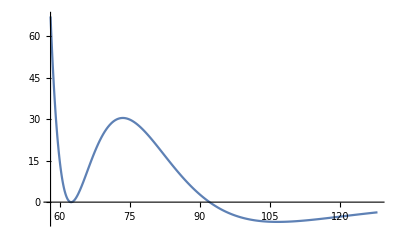

```mathematica
vala=2Pi/100;
valb=2Pi/99;
valA=1;
valB=-1.03;

init=58;
Plot[V*10^(15)/.{a->vala,b->valb,A->valA,B->valB},{ReT,init,init+70},WorkingPrecision->100,PlotPoints->200]
```

```mathematica
A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))/.{a->vala,b->valb,A->valA,B->valB}
```

0.000198152

KKLT

```mathematica
ClearAll;

zero[x_]=0;

W=w0+A Exp[-a T];
W̄=W/.{T->T̄};
K=-3Log[T+T̄];

Subscript[W, T]=D[W,T]/.{OverBar'->zero,OverBar''->zero};

Subscript[K, T]=D[K,T]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T̄]=D[K,T̄]/.{OverBar'->zero,OverBar''->zero};
Subscript[K, T T̄]=D[K,T,T̄]/.{OverBar'->zero,OverBar''->zero};
DTW=Subscript[W, T]+Subscript[K, T]*W;
OverBar[DTW]=DTW/.{T->T̄,T̄->T};

vtemp=Exp[K]*((Subscript[K, T T̄])^(-1)*(DTW)*(OverBar[DTW])-3W*W̄);
Print["V=",vtemp];

V=FullSimplify@ComplexExpand[vtemp/.{T->ReT+I ImT,T̄->ReT-I ImT}];
Print["V=",V];
```

V=(-3 (A ⅇ^(-a T)+w0) (A ⅇ^(-a T̄)+w0)+1/3 (T+T̄)^2 (-a A ⅇ^(-a T)-(3 (A ⅇ^(-a T)+w0))/(T+T̄)) (-a A ⅇ^(-a T̄)-(3 (A ⅇ^(-a T̄)+w0))/(T+T̄)))/(T+T̄)^3

V=(a A ⅇ^(-2 a ReT) (A (3+a ReT)+3 ⅇ^(a ReT) w0 Cos[a ImT]))/(6 ReT^2)

```mathematica
V=FullSimplify[V/.{ImT->Pi/a,w0->Abs[A Abs[a A/(b B)]^(a/(b-a))+B Abs[a A/(b B)]^(b/(b-a))]}];
Print["V=",V];
```

V=(a A ⅇ^(-2 a ReT) (A (3+a ReT)-3 ⅇ^(a ReT) Abs[A Abs[(a A)/(b B)]^(a/(-a+b))+B Abs[(a A)/(b B)]^(b/(-a+b))]))/(6 ReT^2)

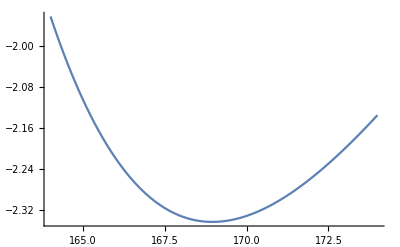

```mathematica
vala=2Pi/100;
valb=2Pi/99;
valA=1;
valB=-1.03;

init=164;
Plot[V*10^(15)/.{a->vala,b->valb,A->valA,B->valB},{ReT,init,init+10},WorkingPrecision->100,PlotPoints->200]
```

メゾンMを入れたポテンシャルのmoduli stabilization